```mathematica
SetDirectory[NotebookDirectory[]]
```

/data2/users/sanderson/Research/KLStats/Isochrone/NoErrors/PermutationMethod

```mathematica
caption[ns_]:=Style[Text[Framed["N="<>ToString[ns]],Scaled[{0.8,0.12}],Background->White],FontSize->24,FontFamily->"Helvetica"]
```

```mathematica
SetOptions[ListContourPlot,Options[ListContourPlot]];
SetOptions[ListContourPlot,InterpolationOrder->1,ColorFunction->"SolarColors",ImageSize->400,PlotRange->{0,3.4},(*PlotRange->{1.2,2.5},ContourStyle->Thick,*)Contours->Range[0,3.4,0.2],FrameStyle->Directive[FontFamily->"Helvetica",FontSize->20],Axes->True,AxesOrigin->{12.2,8.0},AxesStyle->Thick,PlotRangePadding->None,ImagePadding->0,Frame->True,Ticks->None,ContourLabels->None(*(Style[Text[#3,{#1,#2}],Bold,White,FontFamily->"Helvetica",FontSize->16]&)*)];
```

Conversion factor between km/s and kpc/Myr to a zillion (16) sigfigs

```mathematica
kmsTokpcMyr=0.001022729843472133;
```

For loop in parallel

```mathematica
Mt0=5.2;
bt0=0.0;
dM=0.2;
db=0.2;
MtMax=19.2;
btMax=16.0;
```

```mathematica
((MtMax-Mt0)/dM)((btMax-bt0)/db)
```

5600.

```mathematica
ParallelEvaluate[$ProcessID]
```

{22474,22595,22713,22830}

```mathematica
ParallelEvaluate[$MachineName]
```

{galileo,galileo,galileo,galileo}

```mathematica
ParallelEvaluate[Install["/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math"]]
```

{LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math,10,2],LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math,10,2],LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math,10,2],LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math,10,2]}

```mathematica
<<streams5tot100.mx
```

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{truePositions,trueVelocities}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Nstars/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample= nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,Mt0,MtMax,dM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{2.28465,{5751,3}}

```mathematica
DumpSave["KL100.mx",KLStats];
```

```mathematica
Max[KLStats[[All,3]]]
```

3.32568

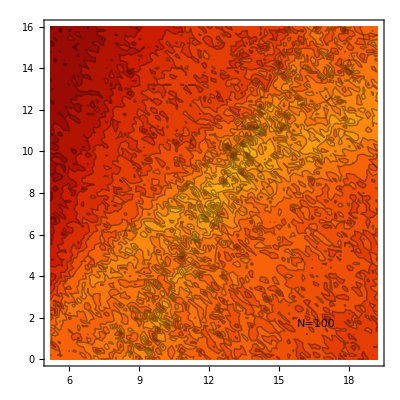

```mathematica
<<KL100.mx
p100=ListContourPlot[KLStats,Epilog->caption[100]]
```

```mathematica
<<streams5tot300.mx
```

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{truePositions,trueVelocities}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Nstars/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample= nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,Mt0,MtMax,dM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{1.87971,{5751,3}}

```mathematica
DumpSave["KL300.mx",KLStats];
```

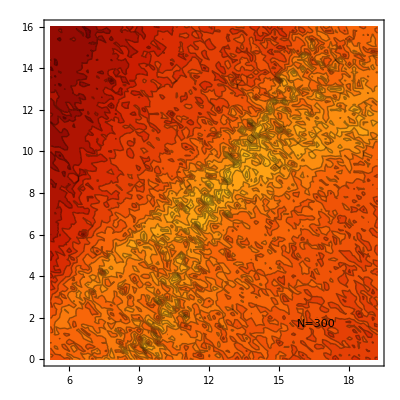

```mathematica
<<KL300.mx
p300=ListContourPlot[KLStats,Epilog->caption[300]]
```

```mathematica
<<streams5tot1000.mx
```

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{truePositions,trueVelocities}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Nstars/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample= nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,Mt0,MtMax,dM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{82.3785,{5751,3}}

```mathematica
DumpSave["KL1000.mx",KLStats];
```

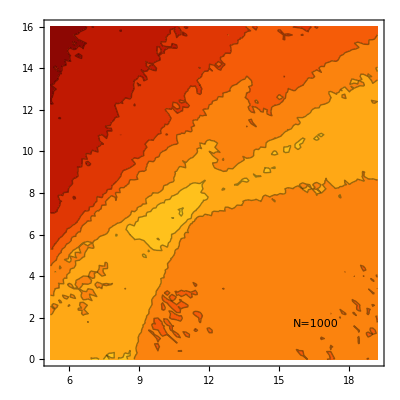

```mathematica
<<KL1000.mx
p1k=ListContourPlot[KLStats,Epilog->caption[1000]]
```

```mathematica
<<streams5tot3000.mx
```

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{truePositions,trueVelocities}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Nstars/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample= nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,Mt0,MtMax,dM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{312.591,{5751,3}}

```mathematica
DumpSave["KL3000.mx",KLStats];
```

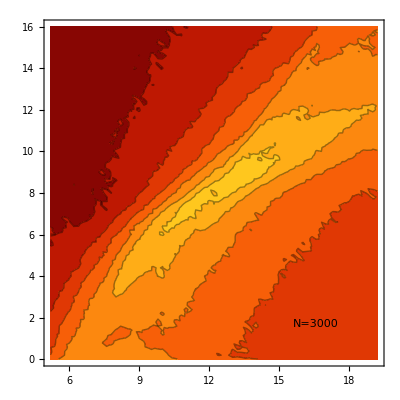

```mathematica
<<KL3000.mx
p3k=ListContourPlot[KLStats,Epilog->caption[3000]]
```

```mathematica
<<streams5tot10000.mx
```

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{truePositions,trueVelocities}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Nstars/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample= nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,Mt0,MtMax,dM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{1625.7,{5751,3}}

```mathematica
DumpSave["KL10000.mx",KLStats];
```

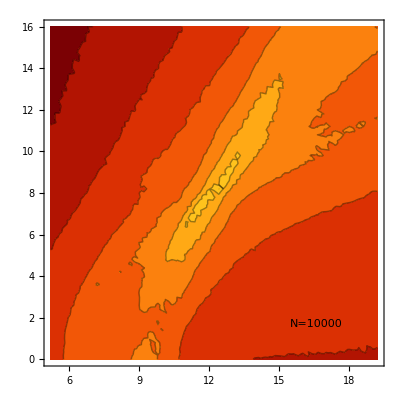

```mathematica
<<KL10000.mx
p10k=ListContourPlot[KLStats,Epilog->caption[10000]]
```

```mathematica
<<streams5tot30000.mx
```

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{truePositions,trueVelocities}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Nstars/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample= nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,Mt0,MtMax,dM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{10552.5,{5751,3}}

```mathematica
DumpSave["KL30000.mx",KLStats];
```

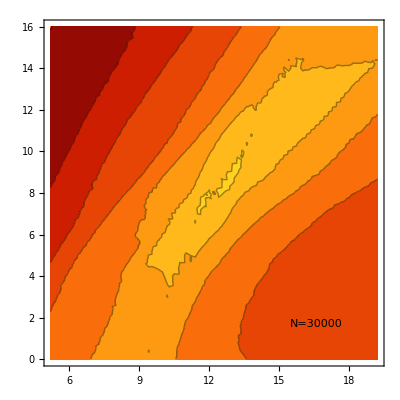

```mathematica
<<KL30000.mx
p30k=ListContourPlot[KLStats,Epilog->caption[30000]]
```

Plots with various numbers of stars

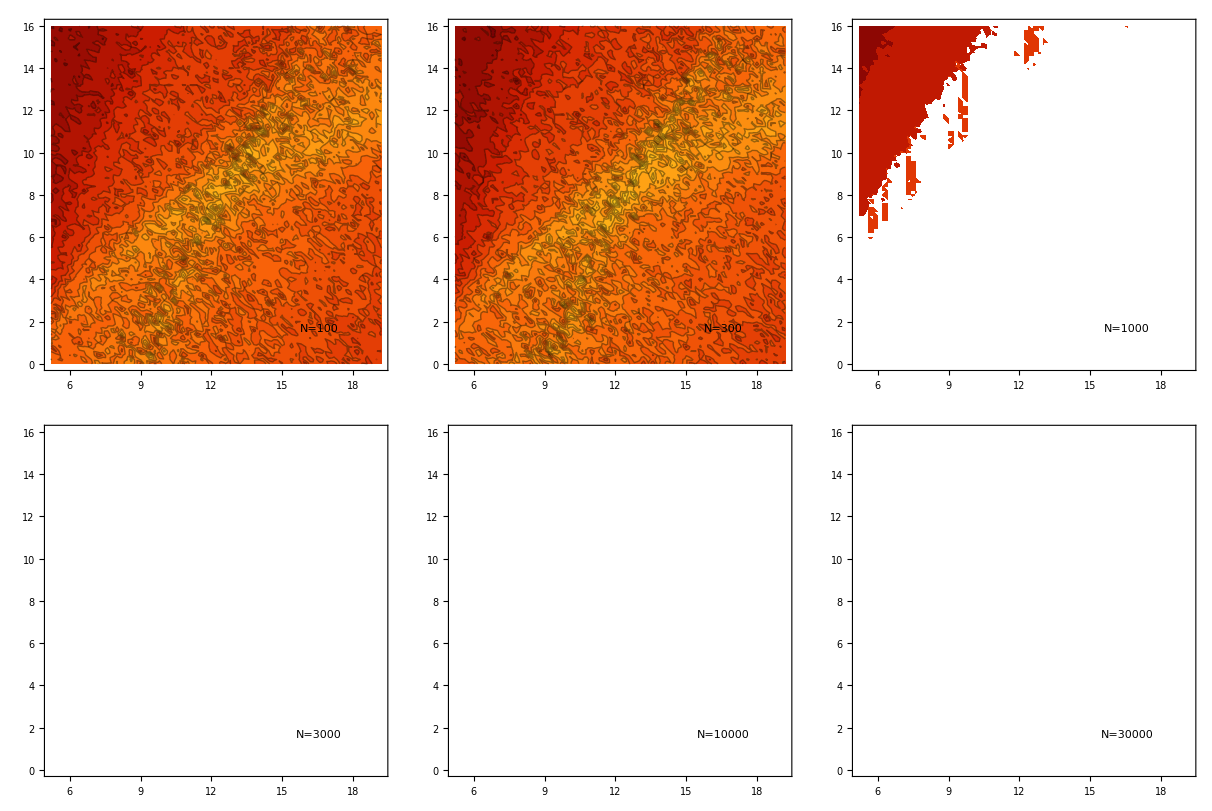

```mathematica
pAll=GraphicsGrid[{{p100,p300,p1k},{p3k,p10k,p30k}},Spacings->0]
```

```mathematica
Export["HowManyStars.png",pAll]
```

HowManyStars.png